# Skydiver equation

```mathematica
DSolve[{V'[t]== g -k V[t] ,V[0]==Subscript[v, 0]},V[t],t]//FullSimplify
```

{{V[t]→(ⅇ^(-k t) ((-1+ⅇ^(k t)) g+k v_0))/k}}

### Example

```mathematica
example=DSolve[{V'[t]== -9.8-0.5V[t] ,V[0]==0},V[t],t]//FullSimplify
```

{{V[t]→-19.6+19.6 ⅇ^(-0.5 t)}}

```mathematica
v[t_]=example[[1,1,2]]
```

-19.6+19.6 ⅇ^(-0.5 t)

```mathematica
Δt:=10
```

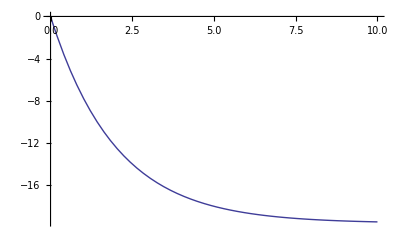

```mathematica
Plot[v[t],{t,0,Δt}]
```